```mathematica
M = {{1,0,0,0,0,0,-1,0,0},
       {0,1,0,0,0,0,-1,0,0},
       {0,0,1,0,0,0,0,-1,0},
       {0,0,0,1,0,0,0,-1,0},
       {0,0,0,0,1,0,0,0,-1},
       {0,0,0,0,0,1,0,0,-1},
       {1,1,0,0,0,0,0,0,0},
       {0,0,1,1,0,0,0,0,0},
      {0,0,0,0,1,1,0,0,0}}
```

{{1,0,0,0,0,0,-1,0,0},{0,1,0,0,0,0,-1,0,0},{0,0,1,0,0,0,0,-1,0},{0,0,0,1,0,0,0,-1,0},{0,0,0,0,1,0,0,0,-1},{0,0,0,0,0,1,0,0,-1},{1,1,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0},{0,0,0,0,1,1,0,0,0}}

```mathematica
M//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0)

```mathematica
Det[M]
```

8

```mathematica
A={
{1,0,0,0,0,0,-1,0,0,0},
{0,1,0,0,0,0,-1,0,0,0},
{0,0,1,0,0,0,0,-1,0,0},
{0,0,0,1,0,0,0,-1,0,0},
{0,0,0,0,1,0,0,0,-1,0},
{1,0,0,0,0,0,0,0,-1,0},
{1,0,1,0,0,0,0,0,0,0},
{0,1,0,1,0,0,0,0,0,0},
{0,0,0,0,1,1,0,0,0,0},
{0,0,1,0,0,0,0,0,0,-1}
}
```

{{1,0,0,0,0,0,-1,0,0,0},{0,1,0,0,0,0,-1,0,0,0},{0,0,1,0,0,0,0,-1,0,0},{0,0,0,1,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0,-1,0},{1,0,0,0,0,0,0,0,-1,0},{1,0,1,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0},{0,0,1,0,0,0,0,0,0,-1}}

```mathematica
A //MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
Det[A]
```

```mathematica
0
```

```mathematica
A={{0,1,-1,0},{0,1,0,-1},{1,0,-1,0},{1,0,0,-1}}
```

{{0,1,-1,0},{0,1,0,-1},{1,0,-1,0},{1,0,0,-1}}

```mathematica
A//MatrixForm
```

(0 | 1 | -1 | 0
0 | 1 | 0 | -1
1 | 0 | -1 | 0
1 | 0 | 0 | -1)

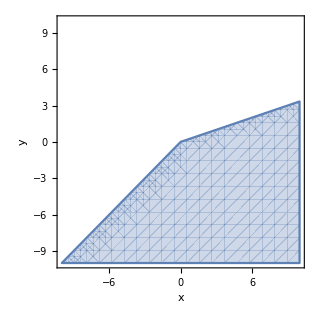

```mathematica
RegionPlot[
{3y-x<=0 &&y-x<=0},
{x,-10,10},
{y,-10,10},
Axes->True,
AxesLabel->{"x","y"}
]
```

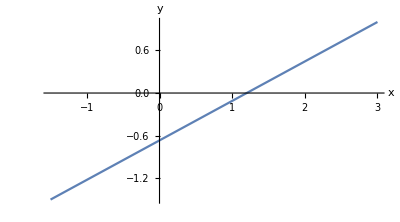

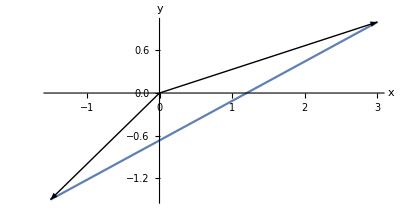

```mathematica
v={3,1};(*Replace v1,v2 with the actual components of vector v*)w={-1.5,-1.5};(*Replace w1,w2 with the actual components of vector w*)plane = ParametricPlot[a*v+(1-a)* w,{a,0,1},AxesLabel->{"x","y"},PlotRange->All,AspectRatio->Automatic]
vectors=Graphics[{Arrow[{{0,0},v}],Arrow[{{0,0},w}]}];
Show[plane,vectors]
```

```mathematica
.14g
```

```mathematica
Det[{{1,0,-1,0},{0,1,0,-1},{1,0,0,-1},{0,1,-1,0}}]
```

0

```mathematica
{{1,0,-1,0},{0,1,0,-1},{1,0,0,-1},{0,1,-1,0}} // MatrixForm
```

(1 | 0 | -1 | 0
0 | 1 | 0 | -1
1 | 0 | 0 | -1
0 | 1 | -1 | 0)

```mathematica
Det[{
{-1,0,0,0,0,0,+1},
{-1,+1,0,0,0,0,0},
{0,-1,+1,0,0,0,0},
{0,0,+1,-1,0,0,0},
{0,0,0,+1,+1,0,0},
{0,0,0,0,-1,+1,0},
{0,0,0,0,0,-1,+1}}]
```

2

```mathematica
{
{-1,0,0,0,0,0,+1},
{-1,+1,0,0,0,0,0},
{0,-1,+1,0,0,0,0},
{0,0,+1,-1,0,0,0},
{0,0,0,+1,+1,0,0},
{0,0,0,0,-1,+1,0},
{0,0,0,0,0,-1,+1}}//MatrixForm
```

(-1 | 0 | 0 | 0 | 0 | 0 | 1
-1 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 1)

```mathematica
({{-1, 0, 0, 0, 0, 0, 1}, {-1, 1, 0, 0, 0, 0, 0}, {0, -1, 1, 0, 0, 0, 0}, {0, 0, +1, -1, 0, 0, 0}, {0, 0, 0, -1, 1, 0, 0}, {0, 0, 0, 0, -1, 1, 0}, {0, 0, 0, 0, 0, -1, 1}})
```

{{-1,0,0,0,0,0,1},{-1,1,0,0,0,0,0},{0,-1,1,0,0,0,0},{0,0,1,-1,0,0,0},{0,0,0,-1,1,0,0},{0,0,0,0,-1,1,0},{0,0,0,0,0,-1,1}}

```mathematica
Det[{{0,0,1,1},{1,0,-1,0},{0,1,0,-1},{1,-1,0,0}}]
```

-2

```mathematica
{{0,0,1,1},{1,0,-1,0},{0,1,0,-1},{1,-1,0,0}}//MatrixForm
```

(0 | 0 | 1 | 1
1 | 0 | -1 | 0
0 | 1 | 0 | -1
1 | -1 | 0 | 0)

```mathematica
a=1
b=2
f[x1_,x2_]:=Min[x1+a,x2+b]
g[x1_,x2_]:=Min[3-x1,7-x2]
h[x1_,x2_]:=f[x1,x2]+g[x1,x2]
Plot3D[h[x1,x2],{x1,-10,10},{x2,-10,10}]
```

1

2

SetDelayed::write: Tag Graphics3D in ()[x1_,x2_] is Protected.

$Failed

```mathematica
Max[Min[y1+c1,y2+c2]+Min[d1-y1+c1p,d2-y2+c2p],{y1,y2}]
```

Max[y1,y2,Min[c1p+d1-y1,c2p+d2-y2]+Min[c1+y1,c2+y2]]

```mathematica
Simplify[Max[y1,y2,Min[c1p+d1-y1,c2p+d2-y2]+Min[c1+y1,c2+y2]]]
```

Max[y1,y2,Min[c1p+d1-y1,c2p+d2-y2]+Min[c1+y1,c2+y2]]

```mathematica
a=1
b=1
f[x1_,x2_]:=Min[x1+a,x2+b]+Min[3-x1,-4-x2]
g = Plot3D[f[x1,x2],{x1,-10,10},{x2,-10,10}, FaceGrids->All]
```

1

1

-Graphics3D-

```mathematica
a=1
b=2
Plot3D[Min[x1+a,x2+b]+Min[2-x1,1-x2],{x1,-10,10},{x2,-10,10}]
```

1

2

-Graphics3D-

```mathematica
A={
{-1,0,0,0,0,0,-1},
{+1,-1,0,0,0,0,0},
{0,+1,+1,0,0,0,0},
{0,0,-1,+1,0,0,0},
{0,0,0,+1,-1,0,0},
{0,0,0,0,+1,+1,0},
{0,0,0,0,0,-1,+1}
}
```

```mathematica
A // MatrixForm
```

(-1 | 0 | 0 | 0 | 0 | 0 | -1
1 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 1)

```mathematica
(_□)_□
```

```mathematica
Det[A]
```

-2